```mathematica
data1={{0,11.26},{100,11.26},{200,11.26},{300,11.25},{400,11.24},{500,11.22},{600,11.21},{700,11.19},{800,11.16},{900,11.14},{1000,11.11},{1100,11.07},{1200,11.04},{1221.5,11.03},{1300,10.31},{1400,10.25},{1500,10.19},{1600,10.12},{1700,10.05},{1800,9.99},{1900,9.91},{2000,9.84},{2100,9.75},{2200,9.67},{2300,9.58},{2400,9.48},{2500,9.38},{2600,9.28},{2700,9.17},{2800,9.05},{2900,8.93},{3000,8.80},{3100,8.66},{3200,8.51},{3300,8.36},{3400,8.20},{3480,8.06}};
```

```mathematica
nlm1=NonlinearModelFit[data, a^2 -b^2 x^2,{a,b},x]
```

FittedModel[11.1502-2.69692×10^-7 x^2]

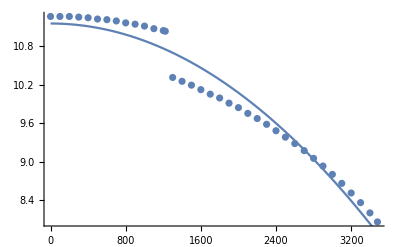

```mathematica
Show[ListPlot[data],Plot[nlm1[x],{x,0,3480}]]
```

```mathematica
data2={{3480,13.72},{3500,},{3600,},{3700,},{3800,},{3900,},{4000,},{4100,},{4200,},{4300,},{4400,},{4500,},{4600,},{4700,},{4800,},{4900,},{5000,},{5100,},{5200,},{5300,},{5400,},{5500,},{5600,},{5701,}}
```